```mathematica
ClearAll["Global`*"]
```

```mathematica
dX = r X[t](1- X[t]/k)-c X[t]Y[t]/(b + X[t])
```

r X[t] (1-X[t]/k)-(c X[t] Y[t])/(b+X[t])

```mathematica
dY = -m Y[t]+a X[t]Y[t]/(b + X[t])
```

-m Y[t]+(a X[t] Y[t])/(b+X[t])

```mathematica
sys1=Collect[FullSimplify[{dX c3/c1,dY c3/c2} /.{X[t]->x[t]c1, Y[t]->y[t]c2}],{x[t],y[t]},FullSimplify]
```

{c3 x[t] (r-(c1 r x[t])/k-(c c2 y[t])/(b+c1 x[t])),-(c3 (b m+c1 (-a+m) x[t]) y[t])/(b+c1 x[t])}

```mathematica
sys2=FullSimplify[(sys1/.{c3->1/r})/.{c1->b}/.{c2->b r/ c}/.{b -> β k}/.{m->r δ}/.{a->r α},Assumptions->{a>0,b>0,c>0,m>0}]
```

{-(x[t] ((1+x[t]) (-1+β x[t])+y[t]))/(1+x[t]),-((δ+(-α+δ) x[t]) y[t])/(1+x[t])}

```mathematica
dx = sys2[[1]]
```

-(x[t] ((1+x[t]) (-1+β x[t])+y[t]))/(1+x[t])

```mathematica
dy = sys2[[2]]
```

-((δ+(-α+δ) x[t]) y[t])/(1+x[t])

```mathematica
FullSimplify[Solve[{dx==0,dy==0},{x[t],y[t]}]]
```

{{x[t]→1/β,y[t]→0},{x[t]→δ/(α-δ),y[t]→(α (α-(1+β) δ))/(α-δ)^2},{x[t]→0,y[t]→0}}

```mathematica
FullSimplify[Reduce[{δ/(α-δ)>0,(α (α-(1+β) δ))/(α-δ)^2>0,α>0,β>0,δ>0}],Assumptions->{α>0,β>0,δ>0}]
```

α>δ+β δ

```mathematica
n1=ExpandAll[y[t]/.Solve[dx/x[t]==0,y[t]][[1]]]
```

1+x[t]-β x[t]-β x[t]^2

```mathematica
Solve[1+x[t]-β x[t]-β x[t]^2==0]
```

{{x[t]→-1},{x[t]→1/β}}

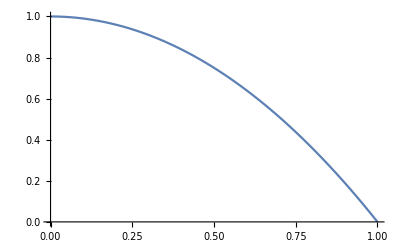

```mathematica
Plot[n1/.{β->1},{x[t],0,1}]
```

```mathematica
n2=ExpandAll[x[t]/.Solve[dy/y[t]==0,x[t]][[1]]]
```

δ/(α-δ)

```mathematica
J11=FullSimplify[D[dx,x[t]]]
```

1-2 β x[t]-y[t]/(1+x[t])^2

```mathematica
J12=FullSimplify[D[dx,y[t]]]
```

-1+1/(1+x[t])

```mathematica
J21=FullSimplify[D[dy,x[t]]]
```

(α y[t])/(1+x[t])^2

```mathematica
J22=FullSimplify[D[dy,y[t]]]
```

-δ+(α x[t])/(1+x[t])

```mathematica
J ={{J11, J12},{J21,J22}}
```

{{1-2 β x[t]-y[t]/(1+x[t])^2,-1+1/(1+x[t])},{(α y[t])/(1+x[t])^2,-δ+(α x[t])/(1+x[t])}}

```mathematica
M=FullSimplify[J/.{x[t]->δ/(α-δ),y[t]->(α (α-(1+β) δ))/(α-δ)^2},Assumptions->{α>0,β>0,δ>0, α>δ(1+β)}]
```

{{2 β+((1+β) δ)/α+(2 α β)/(-α+δ),-δ/α},{α-(1+β) δ,0}}

```mathematica
FullSimplify[Tr[M],Assumptions->{α>δ>0}]
```

2 β+((1+β) δ)/α+(2 α β)/(-α+δ)

```mathematica
FullSimplify[Det[M],Assumptions->{α>δ>0}]
```

(δ (α-(1+β) δ))/α

```mathematica
FindInstance[{Tr[M]<0,α>0,β>0,δ>0, α>δ(1+β)},{α,β,δ}]
```

{{α→2,β→5/8,δ→1}}

```mathematica
FindInstance[{Tr[M]>0,α>0,β>0,δ>0, α>δ(1+β)},{α,β,δ}]
```

{{α→2,β→1/4,δ→1}}

```mathematica
FullSimplify[Reduce[{Det[M]>0,α>0,β>0,δ>0, α>δ(1+β)}],Assumptions->{α>0,β>0,δ>0, α>δ(1+β)}]
```

True

```mathematica
FullSimplify[Reduce[{Tr[M]<0,α>0,β>0,δ>0, α>δ(1+β)}],Assumptions->{α>0,β>0,δ>0, α>δ(1+β)}]
```

```mathematica
FullSimplify[Reduce[{α<δ+β (α+δ),α>0,β>0,δ>0, α>δ(1+β)}],Assumptions->{α>0,β>0,δ>0, α>δ(1+β)}]
```

α<δ+β (α+δ)

```mathematica
Solve[{xs==δ/(α-δ),ys==(α (α-(1+β) δ))/(α-δ)^2},{α,β}][[1]]
```

{α→((1+xs) δ)/xs,β→(1+xs-ys)/(xs (1+xs))}

```mathematica
Solve[xs==δ/(α-δ),δ]
```

{{δ→(xs α)/(1+xs)}}

```mathematica
FullSimplify[(α (α-(1+β) δ))/(α-δ)^2/.δ->(xs α)/(1+xs)]
```

1+xs-xs (1+xs) β

```mathematica
M2=FullSimplify[M/.{α->((1+xs) δ)/xs,β->(1+xs-ys)/(xs (1+xs))}]
```

{{-1+((1+2 xs) ys)/(1+xs)^2,-1+1/(1+xs)},{(ys δ)/(xs+xs^2),0}}

```mathematica
Det[M2]
```

(xs ys δ)/((1+xs) (xs+xs^2))

```mathematica
Tr[M2]
```

-1+((1+2 xs) ys)/(1+xs)^2

```mathematica
Reduce[{Tr[M2]>0,xs>0,ys>0},xs]
```

ys>1&&0<xs<-1+ys+√(-ys+ys^2)

```mathematica
FullSimplify[Eigenvalues[M2],Assumptions->{xs>0,ys>0,δ>0}]
```

{-(1+xs (2+xs-2 ys)-ys+√(((1+xs)^2-(1+2 xs) ys)^2-4 (1+xs)^2 ys δ))/(2 (1+xs)^2),(-1-xs (2+xs-2 ys)+ys+√(((1+xs)^2-(1+2 xs) ys)^2-4 (1+xs)^2 ys δ))/(2 (1+xs)^2)}

```mathematica
FullSimplify[Eigenvalues[M],Assumptions->{α>0,β>0,δ>0,α>δ(1+β)}]
```

{-(α (-1+β) δ+(1+β) δ^2+√(δ (δ (α (-1+β)+δ+β δ)^2-4 α (α-δ)^2 (α-(1+β) δ))))/(2 α (α-δ)),(-α (-1+β) δ-(1+β) δ^2+√(δ (δ (α (-1+β)+δ+β δ)^2-4 α (α-δ)^2 (α-(1+β) δ))))/(2 α (α-δ))}